Measurements on Quantum States |

Projective Measurementspaclet:Q3/tutorial/MeasurementsOnQuantumStates#1477689096 | Generalized Measurementspaclet:Q3/tutorial/MeasurementsOnQuantumStates#406380704

See also Section 1.3 of the Quantum Workbook (Springer, 2022)https://doi.org/10.1007/978-3-030-91214-7.

In classical mechanics, just like the state of motion, a physical quantity is described by a simple number for a scalar quantity or by a set of numbers for a vector quantity. As such, measurement merely assesses such number(s) and casts technological questions concerning only measuring devices. In quantum mechanics, measurement is totally different and is deeply intermingled into quantum theory itself.

Ketpaclet:Q3/ref/KetQ3 Package Symbol | Represents a computational basis vector
Basispaclet:Q3/ref/BasisQ3 Package Symbol | Constructs a computational basis
Dyadpaclet:Q3/ref/DyadQ3 Package Symbol | Dyadic product of state vectors
Measurementpaclet:Q3/ref/MeasurementQ3 Package Symbol | Represents a Pauli measurement
MeasurementOddspaclet:Q3/ref/MeasurementOddsQ3 Package Symbol | Analyses a Pauli measurement
SchmidtDecompositionpaclet:Q3/ref/SchmidtDecompositionQ3 Package Symbol | Returns the Schmid decomposition of a quantum state for a bi-partite system
PartialTracepaclet:Q3/ref/PartialTraceQ3 Package Symbol | Partial trace over a part of the system
VonNeumannEntropypaclet:Q3/ref/VonNeumannEntropyQ3 Package Symbol | Returns the von Neuman entropy of a quantum state
Multiplypaclet:Q3/ref/MultiplyQ3 Package Symbol | Noncommutative multiplication
Matrixpaclet:Q3/ref/MatrixQ3 Package Symbol | Returns the matrix representation of a vecotr or an operator in the compputation basis
ExpressionForpaclet:Q3/ref/ExpressionForQ3 Package Symbol | Constructs a ket or an operator expression from a matrix representation

Q3 functions related to what is discussed in this document.

Make sure that the Q3 package is loaded to use the demonstrations in this documentation.

```mathematica
<<Q3`
```

Throughout this document, symbol S will be used to denote qubits and Pauli operators on them. Similarly, symbol c will be used to denote complex-valued coefficients.

```mathematica
Let[Qubit,S]
Let[Complex,c]
```

Projective Measurements

Postulate 3. A physical quantity is described by an “observable”—a Hermitian operator. Upon measurement of an observable A, the outcome is probabilistically selected from one of the eigenvalues a of A. When the system is in the state |ψ⟩ right before measurement, the probability of a particular outcome a is given by P_a=(|aψ|)^2, where a is the eigenstate of A belonging to the eigenvalue a. Right after measurement, the state “collapses” to the eigenstate a corresponding to outcome a.

The postulate points out several striking features that distinguish quantum mechanics from classical mechanics. First, a measurable physical quantity (i.e., an observable) is not described by a simple number but by an operator acting on the vectors that describe the quantum states of the system (see Postulate 1).

Second, measurement brings about a sudden collapse of the state vector whereby an unavoidable disturbance by mere measurement causes obvious obstacles to naively examining quantum states. At the same time, this opens new opportunities for practical applications such as to achieve secure quantum communications. Furthermore, this collapse is a peculiar dynamics of quantum states and an alternative to that governed by the Schrödinger equation (Postulate 2), which turns out to be useful to construct measurement-based quantum computing architectures. Even in the common dynamical schemes of quantum computation, measurement is often used to initialize the quantum registers to the logical basis states. Combined with classical communications, measurement also enriches available gate operations.

Third, the postulate makes it clear that even if the state vector |ψ⟩ is known, which comprises the complete description of the state according to Postulate 1, one cannot infer the measurement results even in principle, but only the probabilities of possible outcomes. The description is inherently statistical, and one needs to measure an ensemble of identically prepared systems to extract the value of an observable in terms of its statistical moments such as the expectation value. Given a state vector |ψ⟩, the expectation value of operator A is obtained by using elementary theory of probability,

⟨A⟩=∑_a a P_a=∑_a ψaaaψ=ψAψ .

For demonstration, consider a two-level system (qubit), the Hilbert space of which is spanned by two computational basis states.

```mathematica
bs=Basis[S];
bs//KetRegulate
```

{0_S,1_S}

Suppose that the system is in the following state.

```mathematica
ket=bs.{1,I Sqrt[2]}/Sqrt[3];
ket//KetRegulate
```

(0_S+ⅈ √2 1_S)/(√3)

We are interested in the measurement of the Pauli Z operator. Before performing the measurement, analyze the measurement outcomes and corresponding post-measurement states.

```mathematica
MeasurementOdds[ket,S[3]]//Map[Simplify]//KetRegulate
```

<|0→{1/3,0_S},1→{2/3,ⅈ 1_S}|>

Now perform the measurement. Here shown are the post-measurement states resulting from different measurement instances. Every time measurement is performed on the same state, the state "collapses" into different states, determined probabilistically.

```mathematica
Table[Measurement[S[3]][ket],10]//KetRegulate
```

{0_S,ⅈ 1_S,ⅈ 1_S,ⅈ 1_S,ⅈ 1_S,ⅈ 1_S,ⅈ 1_S,0_S,ⅈ 1_S,ⅈ 1_S}

This shows the measurement statistics when one repeats the measurement 500 times. As we can see from the above analysis using MeasurementOddspaclet:Q3/ref/MeasurementOddsQ3 Package Symbol, the measurement outcomes are distributed approximately according to probabilities 1/3 and 2/3.

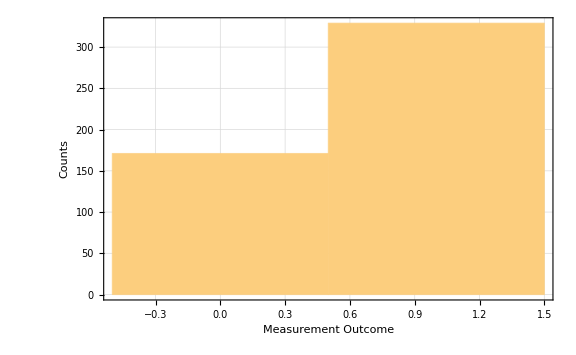

```mathematica
out=Table[Measurement[S[3]][ket];Readout[S[3]],500];
Histogram[out,FrameLabel->{"Measurement Outcome","Counts"}]
```

This time, suppose that we are interested in the measurement of the Pauli X operator (instead of Pauli Y)  
on the same state.

```mathematica
MeasurementOdds[ket,S[1]]//Map[Simplify]//KetRegulate
```

<|0→{1/2,((2 ⅈ+√2) (0_S+1_S))/(2 √3)},1→{1/2,((-2 ⅈ+√2) (0_S-1_S))/(2 √3)}|>

Performing the measurement repeatedly results in different post-measurement states, both of which are eigenstates of the Pauli X.

```mathematica
Table[Measurement[S[1]][ket],10]//KetRegulate
```

{(ⅈ/(√3)+1/(√6)) 0_S+(ⅈ/(√3)+1/(√6)) 1_S,(-ⅈ/(√3)+1/(√6)) 0_S+(ⅈ (ⅈ+√2) 1_S)/(√6),(-ⅈ/(√3)+1/(√6)) 0_S+(ⅈ (ⅈ+√2) 1_S)/(√6),(-ⅈ/(√3)+1/(√6)) 0_S+(ⅈ (ⅈ+√2) 1_S)/(√6),(-ⅈ/(√3)+1/(√6)) 0_S+(ⅈ (ⅈ+√2) 1_S)/(√6),(ⅈ/(√3)+1/(√6)) 0_S+(ⅈ/(√3)+1/(√6)) 1_S,(-ⅈ/(√3)+1/(√6)) 0_S+(ⅈ (ⅈ+√2) 1_S)/(√6),(ⅈ/(√3)+1/(√6)) 0_S+(ⅈ/(√3)+1/(√6)) 1_S,(-ⅈ/(√3)+1/(√6)) 0_S+(ⅈ (ⅈ+√2) 1_S)/(√6),(-ⅈ/(√3)+1/(√6)) 0_S+(ⅈ (ⅈ+√2) 1_S)/(√6)}

This shows the measurement statistics when one repeats the measurement 500 times.

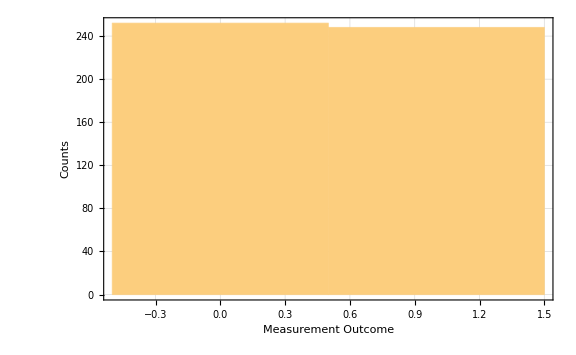

```mathematica
out=Table[Measurement[S[1]][ket];Readout[S[1]],500];
Histogram[out,FrameLabel->{"Measurement Outcome","Counts"}]
```

### No-Cloning Theorem

A closely related feature of quantum states is reflected in the no-cloning theorem (Wootters and Zurek, 1982). The theorem dictates that it is impossible to make a copy of an unknown quantum state. If it were possible, one could produce a bunch of identical copies of the same quantum state. Then, measurements of different incompatible observables (such as conjugate variables) on the copies would reveal precise information regarding the quantum state, violating the uncertainty principle. Cloning of an (unknown) quantum state would also allow faster-than- light communication. Furthermore, the no-cloning nature of quantum states is one of the key features of quantum mechanics that provide unconditional security in quantum communication.

A proof of the no-cloning theorem reveals that in the no-cloning nature of quantum state, crucial is the linearity of quantum mechanics.

### Measurements on Mixed States

In the above statement of the postulate, the system is assumed to be in a pure state initially, and the statement can be naturally extended to the case of mixed state. When a system is in a mixed state ρ right before the measurement, the probability is given by

P_a=aρa

and the state right after the measurement becomes aa. By virtue of the elementary theory of probability, we observe again that 0≤ρ≤1 and Tr ρ=1 (see Mixed States). Furthermore, the expectation value of the observable is given by

⟨A⟩=∑_a a P_a=∑_a aaρa=Tr A ρ .

### Von Neumann Scheme of Projective Measurements

Von Neumann envisioned an idealistic procedure to perform a projective measurement on physical systems. For this reason, projective measurement is also referred to as a von Neumann measurement. The von Neumann scheme laid the foundation for the quantum theory of measurement, and it has inspired various methods to improve the measurement precision towards the intrinsic limit of quantum mechanics. The von Neumann scheme for projective measurement can be implemented directly in a quantum circuit model. Here, we briefly summarize the procedure.

Suppose that we want to measure a quantity described by a Hermitian operator A. Let a be the eigenvectors with eigenvalues a of A so that A has spectral decomposition

A=∑_a aaa.

The system is in a state |ψ⟩, which is expanded as

ψ=∑_a a ψ_a

in the eigenbasis of A. Typically, the probability distribution P_a:=(|ψ_a|)^2 is supposed to sharply peak around a certain unknown eigenstate a_*, and the measurement is supposed to reveal a_*.

We choose a measuring device with “position” X, which can be directly observed, and we prepare it in an approximate eigenstate |ξ⟩ of X. In terms of eigenstates x with eigenvalue x of X, |ξ⟩ is expanded as

ξ=∫d xxξ(x)

with ξ(x) having a sharp peak around a certain fixed point x0. It will become clear below how a sharper distribution (|ξ(x)|)^2 in the position results in a more accurate measurement. At this stage, ψ⊗ξ is the overall state of the total system containing the system to be measured and the measurement device.

Now couple the observable A in question to the “momentum” P (not X itself) of the measurement device. Note that P and X are canonical conjugates of each other such that [X,P]=ⅈ (recall that we have chosen a unit system such that  ℏ=1). The coupling is described by the interaction Hamiltonian

H_int=J P⊗A ,

where J is the coupling strength. One has to let the system and the measurement device interact for a sufficiently long time τ such that the position of the measurement device is distinguished from the initial position. Let g:=J τ be the dimensionless coupling constant. Due to coupling, the total system composed of the system in question and the measurement device evolves over time, which is described by the unitary operator

U_int=exp(-ⅈ g P⊗A) .

This situation is depicted diagrammatically as follows

-Graphics-

It is instructive to expand the interaction unitary operator U int using the spectral decomposition of the observable A as

U_int=∑_a ⅇ^(-ⅈ g a P)⊗aa

The operator T_a:=exp(-ⅈ g a P) represents the translation by an amount g a depending on eigenvalue a of A. To clarify the physical interpretation, we rewrite the interaction
 unitary operator into

U_int=∑_a T_a⊗aa.

This physical picture is further elucidated in the following schematic diagram

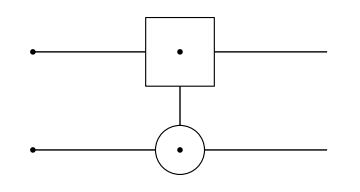

After the interaction, the state vector of the total system becomes

U_int Ψ=∑_a (T_a ξ)⊗(a ψ_a)=∫d x x⊗(∑_a aξ(x-g a)ψ_a).

In general, the final state is an entangled state. The probability to register x out of the measurement on the measurement device is given by

P(x)=∑_a (|ξ(x-g a)|)^2(|ψ_a|)^2.

When the system starts from a definite eigenstate a of A, the system and the measurement device remain separable after the system-measurement device interaction, with its probability distribution determined solely by the given eigenvalue a

P(x)=∑_a (|ξ(x-g a)|)^2.

Manifestly, the measurement accuracy is best in this case. 
As illustrated in Figure 1 below, one can extract eigenvalue a of the observable from the amount of translation g a of the final wave function relative to the initial wave function assuming that coupling strength g is known (it can be calibrated separately).

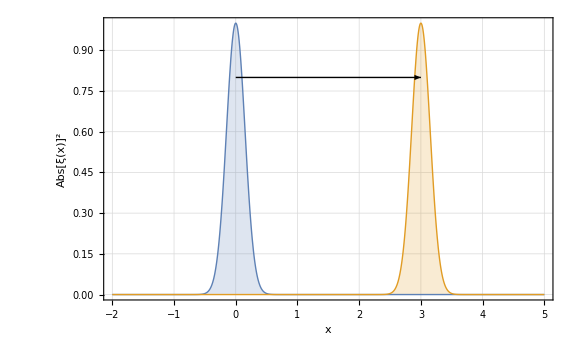

Figure 1. Change in the wave function ξ(x) of the measurement device from the initial state (blue) to the final state (orange) after it interacts with the system. This case illustrates a system in a definite eigenstate a of the observable A under measurement. The amount of translation is given by g a, the coupling constant times the eigenvalue associated with a.

Figure 1 suggests that a sharper initial wave function of the measurement device results in a more precise extraction of the value of a. Roughly speaking, this is indeed one direction of the efforts to improve the precision of measurement (Caves, 1981). An obstacle directly apparent in the above figure to achieve precise measurement is the inherent statistical nature of quantum mechanics. Given that the probability distribution has finite width, any measurement in quantum mechanics should be repeated many times. The statistical error decreases as 1/√N with the increasing number N of repeated measurements. This is called the standard quantum limit. Interestingly, if one prepares a set of measurement devices in a proper entangled state, one can improve the statistical error to 1/N (Giovannetti et al., 2006). This enhanced accuracy due to quantum entanglement is called the Heisenberg limit, and it puts the ultimate limit on the measurement precision that quantum mechanics allows.

Generalized Measurements

Concerning measurement, we introduced Postulate 3 in its usual form as discussed in most textbooks on quantum mechanics. However, in quantum information context and for various reasons to be discussed shortly, it is convenient to provided a generalized form of Postulate 3.

Postulate 3'. A generalized measurement is described by a set of measurement operators M_m corresponding to measurement outcomes m that satisfy the completeness relation

∑_m M_m^†M_m=I.

Suppose that right before the measurement, the system is in the quantum state ρ. Then the probability P_m for outcome m is given by

P_m=Tr M_m ρ M_m^†,

and the state right after the measurement becomes

1/P_m M_m ρ M_m^†=(M_m ρ M_m^†)/(Tr M_m ρ M_m^†).

The projective measurement discussed previously is a special case of the generalized measurement. Suppose that we measure an observable A. In this case, the available measurement outcomes are eigenvalues a of A. The measurement operator corresponding to outcome a is the projection operator aa onto the eigenstate |a⟩ belonging to eigenvalue a.

In general, the physical meaning of the measurement operators M_m is not immediately clear until the specifics of the measurement in question are narrated. It is even more difficult to determine the setup of a physical device for the measurement described by the given set of operators M_m. Nevertheless, one can show that generalized measurements are equivalent to projective measurements (extended to a larger system and supplemented with additional unitary operations). In many applications, however, generalized measurements are more convenient because they are less restrictive.

For example, consider a fixed set of orthogonal quantum states ψ_1, ψ_2, …, ψ_n (not necessarily spanning the Hilbert space). Suppose that a state is drawn from the set. The task is to tell which of the n states it is. We proceed by defining n operators

M_k:=ψ_kψ_k

for k=1,2,…,n and an additional operator

M_0:=I-∑_k M_k.

They satisfy the completeness relation

∑_k M_k^†M_k=I

and describe a measurement. Now when a particular state ψ_k is taken, the probability
P_□ for measurement outcome k is unity because

P_k=ψ_k M_k ψ_k.

### POVM

Postulates 3 and 3' describe not only the probability for a particular measurement outcome but also the post-measurement state corresponding to the outcome after the measurement. However, many experiments probe the system only once, and the state after the measurement is irrelevant. Of primary concern are the probabilities. Often, it is even impossible to assign a post-measurement state to the system. For example, in an experiment to measure the position of photon, the photon is destroyed at the photo-screen, and it is meaningless to ask about the wave function of the photon after the measurement.

As long as one is focused on the probabilities, the description in Postulate 3' can be drastically simplified: Since the trace is invariant under cyclic permutation of the operators, the probability for the outcome m is given by

P_m=Tr M_m ρ M_m^†=Tr M_m^†M_m ρ .

Therefore, as far as the probabilities are concerned, all we need are the operators

E_m:=M_m^†M_m

rather than the measurement operators M_m. Note that M_m may contain far more details that cannot be extracted from E_m. Infinitely many distinct measurement operators can lead to the same E_m. Nevertheless, it is possible to discard certain details in M_m for more compact operators E_m because we do not care about the post-measurement state. By construction, E_m are positive semi-definite operators and satisfy

∑_m E_m=I.

The set {E_m} of such operators is called a positive operator-valued measure or more often a POVM. The individual operators E_m are called POVM elements. For many experiments, the POVM formalism allows far more efficient description of the measurement.

As a non-trivial example of the application of the POVM formalism, let us consider the problem of quantum state discrimination of non-orthogonal quantum states (Bergou et al., 2004; Chefles, 2004). To be specific, suppose that we are given either of the two states

v=0 , 	w=(0+1)/(√2).

We have to figure out which one it is. These two states are not orthogonal, vw!=0, and it is impossible to discriminate them with certainty. Instead, the task is to perform a measurement that tells which of the two, but never misidentifies a wrong state.

Consider a POVM including the following three elements

E_1:=1/(√(1+vw))11,

E_2:=1/(√(1+vw))((0-1)/(√2))((0-1)/(√2)),

E_3:=I-E_1-E_2.

It is straightforward to check that they form a POVM. Suppose that the state v  is given. As it is orthogonal to 1, the measurement outcome m=1—corresponding to the POVM element E_1—never occurs. This means that once m=2—corresponding to E_2—occurs, the state must be w. For the same reason, the result m=1 implies that the state is definitely v. Of course, it is possible to obtain the outcome m = 3, in which case the measurement reveals nothing. However, the important point is that there is no chance to make a mistake.

| Related Guides
▪Quantum Information Systems

| Related Tech Notes
▪The Postulates of Quantum Mechanics
▪Computational Model of Measurement
▪Measurements as Quantum Operations
▪The No-Cloning Theorem
▪Quantum Phase Estimation
▪Quantum Information Systems with Q3

| Related Links
▪W. K. Wootters and W. H. Zurek, Nature 299, 802 (1982)https://doi.org/10.1038/299802a0, "A Single Quantum Cannot be Cloned."
▪J. A. Bergou, U. Herzog, and M. Hillery (2004)https://doi.org/10.1007/978-3-540-44481-7_11, “Discrimination of Quantum States,” in Paris and Rehacek (2004)https://doi.org/10.1007/b98673.
▪A. Chefles (2004)https://doi.org/10.1007/978-3-540-44481-7_12, “Quantum States: Discrimination and Classical Information Transmission. A Review of Experimental Progress,” in Paris and Rehacek (2004)https://doi.org/10.1007/b98673.
▪M. Paris and J. Rehacek, eds., Quantum State Estimation (Springer Berlin Heidelberg, 2004)https://doi.org/10.1007/b98673.
▪M. Nielsen and I. L. Chuang (2022)https://doi.org/10.1017/CBO9780511976667, Quantum Computation and Quantum Information (Cambridge University Press, 2011).
▪Mahn-Soo Choi (2022)https://doi.org/10.1007/978-3-030-91214-7, A Quantum Computation Workbook (Springer, 2022).